# The electrocalorics of PbSr_2 Ti_2 O_7:

## Options:

### Plot options:

```mathematica
a= "Rainbow";b= 300;q=250;plotFont={FontWeight->"Bold",FontSize->12};(*rainbow looks good but it would be nice to have a blue to white colorscheme that I saw a few weeks ago... *)
```

## Load ab initio data into memory

### Load DFT data into memory using a specific set of indices

```mathematica
(*"StringFormat"->{"    ","Qx[%]","    ","Qy[%]","    ","Qx[A]","    ","Qy[A]","    ","|Q|[A]","    ","Px[C/m^2]","    ","Py[C/m^2]","       ","|P| [C/m^2]"}*)
(*Need to save as .xlsx first in LibreOffice after cutting the space delimiters with fixed width and then save as .csv, (should give option for "," delimiters, then can open as .csv*)
```

```mathematica
a1pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/1pcComp.csv","Data"];Dimensions[a1pcComp];
a2pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/2pcComp.csv","Data"];Dimensions[a2pcComp];
a1pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/1pcTens.csv","Data"];Dimensions[a1pcTens];
a2pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/2pcTens.csv","Data"];Dimensions[a2pcTens];
aUnstr=Import["/home/john/PSTO_stuff_Byounghak/QPdata/unstrained.csv","Data"];Dimensions[aUnstr];
EgUnstr=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_unstrained.csv","Data"];Dimensions[EgUnstr];
Eg1pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_squeeze1.csv","Data"];Dimensions[Eg1pcComp];
Eg2pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_squeeze2.csv","Data"];Dimensions[Eg2pcComp];
Eg1pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_stretch1.csv","Data"];Dimensions[Eg1pcTens];
Eg2pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_stretch2.csv","Data"];Dimensions[Eg2pcTens];
```

```mathematica
(*Manipulate[{Plot[Nest[Function[t,1/(1+t)],x,j],{x,-3,3}],Nest[Function[t,1/(1+t)],x,j]},{j,3,15,1}] a very cool diversion*)
```

Serge’s data needs the following list index... since we only want Q_(x,y) ≤ 15

```mathematica
list1=Flatten[{Table[j,{j,1,16}],
Table[j,{j,16+12,16+12+14}],
Table[j,{j,16+(2*12)+14,16+(2*12)+14+13}],
Table[j,{j,16+(3*12)+14+13,16+(3*12)+14+13+12}],
Table[j,{j,16+(4*12)+14+13+12,16+(4*12)+14+13+12+11}],
Table[j,{j,16+(5*12)+14+13+12+11,16+(5*12)+14+13+12+11+10}],
Table[j,{j,16+(6*12)+14+13+12+11+10,16+(6*12)+14+13+12+11+10+9}],
Table[j,{j,16+(7*12)+14+13+12+11+10+9,16+(7*12)+14+13+12+11+10+9+8}],
Table[j,{j,16+(8*12)+14+13+12+11+10+9+8,16+(8*12)+14+13+12+11+10+9+8+7}],
Table[j,{j,16+(9*12)+14+13+12+11+10+9+8+7,16+(9*12)+14+13+12+11+10+9+8+7+6}],
Table[j,{j,16+(10*12)+14+13+12+11+10+9+8+7+6,16+(10*12)+14+13+12+11+10+9+8+7+6+5}],
Table[j,{j,16+(11*12)+14+13+12+11+10+9+8+7+6+5,16+(11*12)+14+13+12+11+10+9+8+7+6+5+4}],
Table[j,{j,16+(12*12)+14+13+12+11+10+9+8+7+6+5+4,16+(12*12)+14+13+12+11+10+9+8+7+6+5+4+3}],
Table[j,{j,16+(13*12)+14+13+12+11+10+9+8+7+6+5+4+3,16+(13*12)+14+13+12+11+10+9+8+7+6+5+4+3+2}],
Table[j,{j,16+(14*12)+14+13+12+11+10+9+8+7+6+5+4+3+2,16+(14*12)+14+13+12+11+10+9+8+7+6+5+4+3+2+1}],
Table[j,{j,16+(15*12)+14+13+12+11+10+9+8+7+6+5+4+3+2+1,16+(15*12)+14+13+12+11+10+9+8+7+6+5+4+3+2+1}]
}];
```

```mathematica
pxUnstr =Table[aUnstr[[k,6]],{k,list1}];
pyUnstr = Table[aUnstr[[k,7]],{k,list1}];
px1pcComp=Table[a1pcComp[[k,6]],{k,list1}];
py1pcComp=Table[a1pcComp[[k,7]],{k,list1}]; 
px1pcTens=Table[a1pcTens[[k,6]],{k,list1}];
py1pcTens=Table[a1pcTens[[k,7]],{k,list1}]; 
px2pcComp=Table[a2pcComp[[k,6]],{k,list1}];
py2pcComp=Table[a2pcComp[[k,7]],{k,list1}];
px2pcTens=Table[a2pcTens[[k,6]],{k,list1}];py2pcTens=Table[a2pcTens[[k,7]],{k,list1}];
```

### Volume dependence on strain

To convert Rydbergs to Joules, we first need the volume of the unit cell. We can fit this using the data in the DFT data. Note that the adata and cdata are in Angstroms. 0.01 represents unitless biaxial tension (+1% of the lattice constant a.)

```mathematica
adata={{-0.02,7.140671*0.529177249},{-0.01,7.213535*0.529177249},{0,7.286399*0.529177249},{0.01,7.359263*0.529177249},{0.02,7.432127*0.529177249}};adatafit=LinearModelFit[adata,{1,ϵ},ϵ];adatafit[{"RSquared"}];Normal[adatafit]
```

3.8558+3.8558 ϵ

```mathematica
cdata={{-0.02,7.140671 5.396907*0.529177249},{-0.01,7.213535 5.301357*0.529177249},{0,7.286399 5.209367*0.529177249},{0.01,7.359263 5.12151*0.529177249},{0.02,7.432127 5.03693*0.529177249}};cdatafit=LinearModelFit[cdata,{1,ϵ},ϵ];cdatafit[{"RSquared"}];Normal[cdatafit]
```

20.0942-14.5833 ϵ

```mathematica
alattice[ϵ_]:=3.855796577936351+3.8557971071135935 ϵ;clattice[ϵ_]:=20.094154572223633-14.583346715316246 ϵ; Vunit[ϵ_]:=alattice[ϵ]^2 clattice[ϵ] (10^-30);
```

```mathematica
Vdata = Table[{adata[[k,1]],adata[[k,2]]^2*cdata[[k,2]] (10^-30)},{k,1,5}];Vdatalistplot=ListPlot[Vdata];
```

```mathematica
u=Plot[Vunit[x],{x,-0.02,0.02},Frame->True,ImageSize->650,PlotStyle->{Red,Thin}];
```

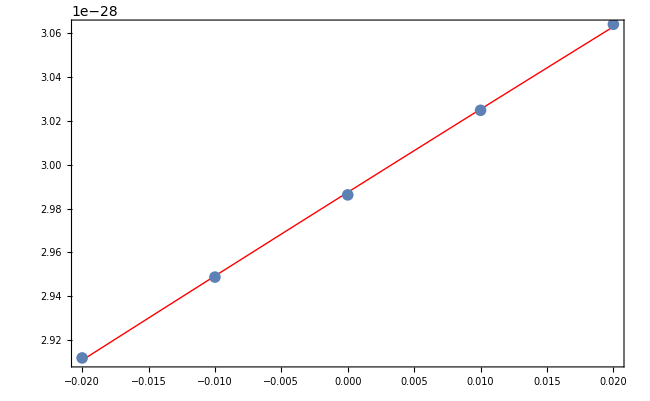

```mathematica
Show[{u,Vdatalistplot}]
```

### Construction of tables of DFT data

Multiply energy by 1/2(2.17*10^-18) and divide by volume of the unit cell converts energy to Joules/m^3.

```mathematica
Tens1pcContdat1=Table[{-px1pcTens[[k]],py1pcTens[[k]],Eg1pcTens[[k,1]]/(2 Vunit[0.01])(2.17896013*10^-18)-Eg1pcTens[[1,1]]/(2 Vunit[0.01])(2.17896013*10^-18)},{k,1,136}];
Tens1pcContdat2=Table[{py1pcTens[[k]],-px1pcTens[[k]],Eg1pcTens[[k,1]]/(2 Vunit[0.01])(2.17896013*10^-18)-Eg1pcTens[[1,1]]/(2 Vunit[0.01])(2.17896013*10^-18)},{k,1,136}];
Tens2pcContdat1=Table[{-px2pcTens[[k]],-py2pcTens[[k]],Eg2pcTens[[k,1]]/(2Vunit[0.02])(2.17896013*10^-18)-Eg2pcTens[[1,1]]/(2 Vunit[0.02])(2.17896013*10^-18)},{k,1,136}];
Tens2pcContdat2=Table[{-py2pcTens[[k]],-px2pcTens[[k]],Eg2pcTens[[k,1]]/(2 Vunit[0.02])(2.17896013*10^-18)-Eg2pcTens[[1,1]]/(2 Vunit[0.02])(2.17896013*10^-18)},{k,1,136}];
Comp1pcContdat1=Table[{-px1pcComp[[k]],-py1pcComp[[k]],Eg1pcComp[[k,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)-Eg1pcComp[[1,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)},{k,1,136}];
Comp1pcContdat2=Table[{-py1pcComp[[k]],-px1pcComp[[k]],Eg1pcComp[[k,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)-Eg1pcComp[[1,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)},{k,1,136}];
Comp2pcContdat1=Table[{-px2pcComp[[k]],py2pcComp[[k]],Eg2pcComp[[k,1]]/(2 Vunit[-0.02])(2.17896013*10^-18)-Eg2pcComp[[1,1]]/(2 Vunit[-0.02])(2.17896013*10^-18)},{k,1,136}];
Comp2pcContdat2=Table[{py2pcComp[[k]],-px2pcComp[[k]],Eg2pcComp[[k,1]]/(2Vunit[-0.02])(2.17896013*10^-18)-Eg2pcComp[[1,1]]/(2 Vunit[-0.02])(2.17896013*10^-18)},{k,1,136}];
UnstrContdat1=Table[{pxUnstr[[k]],pyUnstr[[k]],EgUnstr[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)-EgUnstr[[1,1]]/(2 Vunit[0])(2.17896013*10^-18)},{k,1,136}];
UnstrContdat2=Table[{pyUnstr[[k]],pxUnstr[[k]],EgUnstr[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)-EgUnstr[[1,1]]/(2 Vunit[0])(2.17896013*10^-18)},{k,1,136}];
```

### Plot DFT data:

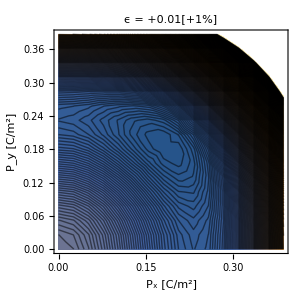
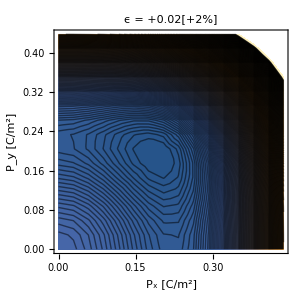

```mathematica
{ListContourPlot[Catenate[{Tens1pcContdat1,Tens1pcContdat2}],ImageSize->b,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","G [J/m^3]"},BaseStyle->plotFont,Contours->q,PlotLabel->"ϵ = +0.01[+1%]",FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"}],ListContourPlot[Catenate[{Tens2pcContdat1,Tens2pcContdat2}],ImageSize->b,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","F [J/m^3]"},BaseStyle->plotFont,Contours->q,PlotLabel->"ϵ = +0.02[+2%]",FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"}]}
```

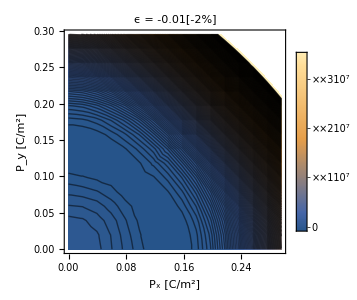
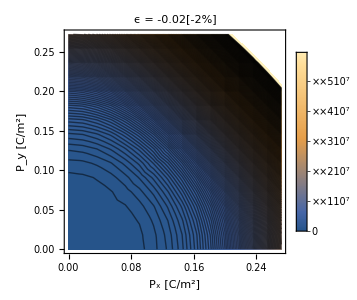

```mathematica
{ListContourPlot[Catenate[{Comp1pcContdat1,Comp1pcContdat2}],ImageSize->b,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","G [J/m^3]"},Contours->q,FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = -0.01[-2%]",ImageSize->b,Contours->q,PlotLegends->True],ListContourPlot[Catenate[{Comp2pcContdat1,Comp2pcContdat2}],ImageSize->b,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","F [J/m^3]"},Contours->q,FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = -0.02[-2%]",ImageSize->b,Contours->q,PlotLegends->True]}
```

### Catenate all DFT data into one set that depends on the strain state:

Let’s add ϵ dependence within the DFT data tables and catenate into one data file.

```mathematica
Tens1pcContdat1ϵ=Table[{-px1pcTens[[k]],py1pcTens[[k]],0.01,Eg1pcTens[[k,1]]/(2 Vunit[0.01])(2.17896013*10^-18)-Eg1pcTens[[1,1]]/(2 Vunit[0.01])(2.17896013*10^-18)},{k,1,136}];
Tens2pcContdat1ϵ=Table[{-px2pcTens[[k]],-py2pcTens[[k]],0.02,Eg2pcTens[[k,1]]/(2Vunit[0.02])(2.17896013*10^-18)-Eg2pcTens[[1,1]]/(2 Vunit[0.02])(2.17896013*10^-18)},{k,1,136}];
Comp1pcContdat1ϵ=Table[{-px1pcComp[[k]],-py1pcComp[[k]],-0.01,Eg1pcComp[[k,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)-Eg1pcComp[[1,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)},{k,1,136}];
Comp2pcContdat1ϵ=Table[{-px2pcComp[[k]],py2pcComp[[k]],-0.02,Eg2pcComp[[k,1]]/(2 Vunit[-0.02])(2.17896013*10^-18)-Eg2pcComp[[1,1]]/(2 Vunit[-0.02])(2.17896013*10^-18)},{k,1,136}];
UnstrContdat1ϵ=Table[{pxUnstr[[k]],pyUnstr[[k]],0,EgUnstr[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)-EgUnstr[[1,1]]/(2 Vunit[0])(2.17896013*10^-18)},{k,1,136}];
```

```mathematica
DFTdata = Catenate[{Comp2pcContdat1ϵ,Comp1pcContdat1ϵ,UnstrContdat1ϵ,Tens1pcContdat1ϵ,Tens2pcContdat1ϵ}];
```

## P-ϵ coupling fit(different functional for each):

### Universal fit form:

```mathematica
UniversalfitForm0[0,Px_,Py_,ϵ_]:=α1(0-120)(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2(Px^4+Py^4)+χ3 Px^2 Py^2)(ϵ)+(χ4(Px^2+Py^2)+χ5(Px^4+Py^4)+χ6 Px^2 Py^2)(ϵ)^2
UniversalfitFormT[T_,Px_,Py_,ϵ_]:=α1(T-120)(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2(Px^4+Py^4)+χ3 Px^2 Py^2)(ϵ)+(χ4(Px^2+Py^2)+χ5(Px^4+Py^4)+χ6 Px^2 Py^2)(ϵ)^2
```

```mathematica
coeffListUniversal={α1,α2,α3,α4,α5,χ1,χ2,χ3,χ4,χ5,χ6};
```

NonlinearModelFit::lmnl: The model -120\ (Px^2 + Py^2)\ α1 + (Px^4 + Py^4)\ α2 + Px^2\ Py^2\ α3 + (Px^6 + Py^6)\ α4 + (Px^4\ Py^2 + Px^2\ Py^4)\ α5 + ϵ\ ((Px^2 + Py^2)\ χ1 + (Px^4 + Py^4)\ χ2 + Px^2\ Py^2\ χ3) + ϵ^2\ ((Px^2 + Py^2)\ χ4 + (Px^4 + Py^4)\ χ5 + Px^2\ Py^2\ χ6) is linear in the parameters {α1, α2, α3, α4, α5, χ1, χ2, χ3, χ4, χ5, χ6}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

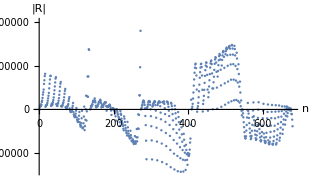
{Universal:, | Estimate | Standard Error | t-Statistic | P-Value
α1 | 1.27129×10^6 | 10236.4 | 124.193 | 3.04336875298×10^-464
α2 | 1.75956×10^9 | 2.51577×10^7 | 69.941 | 7.49711242583×10^-310
α3 | 3.73096×10^9 | 2.82984×10^7 | 131.844 | 6.26174675966×10^-481
α4 | -5.9011×10^8 | 1.44686×10^8 | -4.07857 | 0.0000507736
α5 | -6.5078×10^8 | 1.12584×10^8 | -5.78039 | 1.14322×10^-8
χ1 | -4.17647×10^9 | 7.1573×10^7 | -58.3526 | 1.20274×10^-264
χ2 | -3.68571×10^10 | 1.16358×10^9 | -31.6755 | 3.1832×10^-135
χ3 | -2.51068×10^11 | 1.47679×10^9 | -170.009 | 1.2273354943×10^-552
χ4 | 1.21299×10^11 | 3.43933×10^9 | 35.2683 | 9.21968×10^-155
χ5 | 2.40518×10^12 | 4.77348×10^10 | 50.3863 | 6.5958×10^-230
χ6 | 6.48666×10^12 | 7.53873×10^10 | 86.0445 | 5.19881937034×10^-364,0.999304,-Graphics-}

```mathematica
fitParamUniversal=NonlinearModelFit[DFTdata,UniversalfitForm0[0,Px,Py,ϵ],coeffListUniversal,{Px,Py,ϵ},Method->NMinimize,MaxIterations->Automatic];
fitUniversal[T_,Px_,Py_,ϵ_]:=UniversalfitFormT[T,Px,Py,ϵ]/.fitParamUniversal["BestFitParameters"];
{"Universal:",fitParamUniversal["ParameterTable"],fitParamUniversal["RSquared"],ListPlot[fitParamUniversal["FitResiduals"],AxesLabel->{"n","|R|"},ImageSize->310]}
```

The above shows the errors in the parameters. This can be propagated to ΔT. Next, let’s add the electric field.

```mathematica
fitUniversal[T_,Px_,Py_,ϵ_,Ex_,Ey_]:=fitUniversal[T,Px,Py,ϵ]-Ex Px -Ey Py
```

### Compare FIT and DFT results in contour plots:

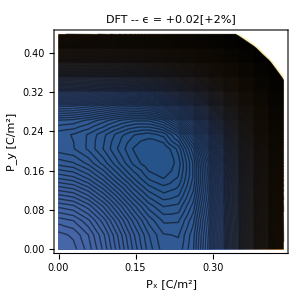
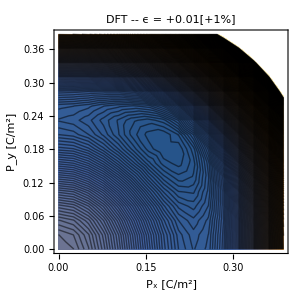
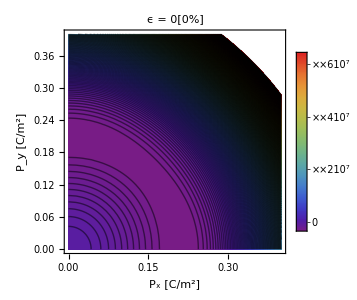
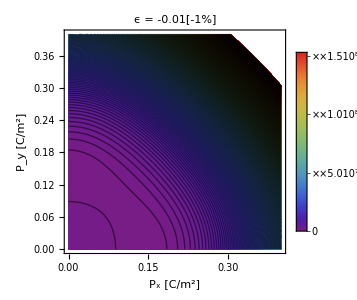
{{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics- -Graphics-,-Graphics- -Graphics-},{-Graphics-}}}

```mathematica
{{{ContourPlot[fitUniversal[0,Px,Py,0.02,0*10^5,0],{Px,0,.4},{Py,0,.4},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"FIT -- ϵ = +0.02[+2%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q,PlotLegends->True],ListContourPlot[Catenate[{Tens2pcContdat1,Tens2pcContdat2}],ImageSize->b,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","G [J/m^3]"},BaseStyle->plotFont,Contours->q,PlotLabel->"DFT -- ϵ = +0.02[+2%]",FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"}]},{ContourPlot[fitUniversal[0,Px,Py,0.01,0*10^5,0],{Px,0,.4},{Py,0,.4},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"FIT -- ϵ = +0.01[+1%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q,PlotLegends->True]},ListContourPlot[Catenate[{Tens1pcContdat1,Tens1pcContdat2}],ImageSize->b,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","G [J/m^3]"},BaseStyle->plotFont,Contours->q,PlotLabel->"DFT -- ϵ = +0.01[+1%]",FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"}]{ContourPlot[fitUniversal[0,Px,Py,0,0*10^5,0],{Px,0,.4},{Py,0,.4},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = 0[0%]",ColorFunction->a,ImageSize->b,Contours->q,PlotLegends->True],ContourPlot[fitUniversal[0,Px,Py,-0.01,0*10^5,0],{Px,0,.4},{Py,0,.4},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = -0.01[-1%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q,PlotLegends->True]},{ContourPlot[fitUniversal[0,Px,Py,-0.02,0*10^5,0],{Px,0,.4},{Py,0,.4},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = -0.02[-2%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q,PlotLegends->True]}}}
```

## Generate equilibrium polarization fields as functions of applied field, misfit strain, and temperature

Create temperature and applied field vectors

```mathematica
ϕ=1;ω=1;Temp=Table[ϕ k,{k,0,250}];appExfield=Table[h,{h,0,120*10^5,ω*10^5}];appEyfield=Table[h,{h,0,120*10^5,ω*10^5}];
```

Create solution grid for different temperatures and applied fields Length[appExfield]*10^5. We want both Ex and Ey in order to find trajectories with the rotating polarization that maximize the electrocaloric effect. Unfortunately, Mathematica doesn’t like .csv files of larger than 4.0 Mb. As each strain state is about 400 Mb, we will have to partition our solves.

```mathematica
fitUniversal[T,Px,Py,ϵ,Ex,Ey]558
```

-Ex Px-Ey Py+3.73096×10^9 Px^2 Py^2+1.75956×10^9 (Px^4+Py^4)-6.5078×10^8 (Px^4 Py^2+Px^2 Py^4)-5.9011×10^8 (Px^6+Py^6)+1.27129×10^6 (Px^2+Py^2) (-120+T)+(-2.51068×10^11 Px^2 Py^2-4.17647×10^9 (Px^2+Py^2)-3.68571×10^10 (Px^4+Py^4)) ϵ+(6.48666×10^12 Px^2 Py^2+1.21299×10^11 (Px^2+Py^2)+2.40518×10^12 (Px^4+Py^4)) ϵ^2

```mathematica
solTens1pcAll[j_,k_]:=ParallelTable[Table[Table[NSolve[{
D[fitUniversal[T,Px,Py,0.01,Ex,Ey],Px]==0,
D[fitUniversal[T,Px,Py,0.01,Ex,Ey],Py],
Px<1,
Py<1,
Px≥0,
Py≥0},{Px,Py}],{T,k,j,ϕ}],{Ex,0,Length[appExfield]*10^5,ω*10^5}],{Ey,0,Length[appEyfield]*10^5,ω*10^5}];
```

### Partitioned solve:

We’ll need 300 of these files. There is no other way unless we port to a lower level programming language. The time it takes to solve this is about 20 minutes per degree Kelvin.

```mathematica
solTens1pcAll1=solTens1pcAll[1,0];Export["/home/john/projects/solTens1pcAll1.csv",solTens1pcAll1,"CSV"]
```

/home/john/projects/solTens1pcAll1.csv

```mathematica
solTens1pcAll2=solTens1pcAll[2,1];Export["/home/john/projects/solTens1pcAll2.csv",solTens1pcAll2,"CSV"]
```

```mathematica
solTens1pcAll3=solTens1pcAll[3,2];Export["/home/john/projects/solTens1pcAll3.csv",solTens1pcAll3,"CSV"]
```

```mathematica
solTens1pcAll4=solTens1pcAll[3,2];Export["/home/john/projects/solTens1pcAll4.csv",solTens1pcAll4,"CSV"]
```

```mathematica
solTens1pcAll5=solTens1pcAll[4,3];Export["/home/john/projects/solTens1pcAll5.csv",solTens1pcAll5,"CSV"]
```

## Load precomputed data into memory(+2% and +1% seem to be a bit off for the moment or are they?.)

```mathematica
solTens2pcImportAll=Import["/home/john/projects/solTens2pcAll.csv","CSV"];Dimensions[solTens2pcImportAll]
```

```mathematica
solTens2pcAll=solTens2pcImportAll//ToExpression ;
```

```mathematica
solUnstrImportAll=Import["/home/john/projects/solUnstrAll.csv","CSV"];Dimensions[solUnstrImportAll] (*load time ~10 min each*)
solTens1pcImportAll=Import["/home/john/projects/solTens1pcAll.csv","CSV"];Dimensions[solTens1pcImportAll] 
solTens2pcImportAll=Import["/home/john/projects/solTens2pcAll.csv","CSV"];Dimensions[solTens2pcImportAll] 
solcomp1pcImportAll=Import["/home/john/projects/solComp1pcAll.csv","CSV"];Dimensions[solcomp1pcImportAll] 
solcomp2pcImportAll=Import["/home/john/projects/solComp2pcAll.csv","CSV"];Dimensions[solcomp2pcImportAll]
```

{201,451}

{201,451}

{201,451}

«2 more identical outputs»

```mathematica
solUnstrAll=solUnstrImportAll//ToExpression ;
solTens1pcAll=solTens1pcImportAll//ToExpression ;
solTens2pcAll=solTens2pcImportAll//ToExpression ;
solComp1pcAll=solcomp1pcImportAll//ToExpression ;
solComp2pcAll=solcomp2pcImportAll//ToExpression ;
```

## Spontaneous polarization as a function of temperature

```mathematica
ListLinePlot[{Table[√((solTens2pcAll[[1,k]][[3,1]])^2+(solTens2pcAll[[1,k]][[3,2]])^2),{k,1,148}],Table[√((solTens1pcAll[[1,k]][[3,1]])^2+(solTens1pcAll[[1,k]][[3,2]])^2),{k,1,144}],Table[√((solUnstrAll[[1,k]][[3,1]])^2+(solUnstrAll[[1,k]][[3,2]])^2),{k,1,120}],Table[√((solComp1pcAll[[1,k]][[3,1]])^2+(solComp1pcAll[[1,k]][[3,2]])^2),{k,1,78}],Table[√((solComp2pcAll[[1,k]][[3,1]])^2+(solComp2pcAll[[1,k]][[3,2]])^2),{k,1,17}]},PlotLegends->Placed[{
"ϵ = +2%",
"ϵ = +1 %",
"ϵ = 0 %",
"ϵ = -1 %",
"ϵ = -2%"},{Scaled[{0.88,0.88}],{0.88,0.88}}],BaseStyle->plotFont,PlotStyle->{{Blue,Thickness[0.0045]},{Blue,DotDashed,Thickness[0.0025]},{Blue,Thickness[0.0025]},{Blue,DotDashed,Thickness[0.0045]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,DotDashed[Tiny],Thickness[0.0025]}},AxesLabel->{"T [K]","|P| [C/m^2]"},ImageSize->700]
```

Part::partw: Part 3 of {{0.0132425, 0.0132425}, {0., 0.}} does not exist.

-Graphics-

```mathematica
solTens2pcAll[[1,138]](*plot of minima and saddle point solutions vs T*)
```

{{0.,0.0581438},{0.0581438,0.},{0.0504506,0.0504506},{0.,0.}}

```mathematica
solTens2pcAll[[1,1]]
```

{{0.,0.219769},{0.219769,0.},{0.191076,0.191076},{0.,0.}}

```mathematica
solTens2pcAll[[15,1]] (*dont worry about rotation of the vector*)
```

{{0.221653,0.},{0.193832,0.19019}}

```mathematica
solTens2pcAll[[1,1]]
```

```mathematica
ListLinePlot[{Table[√((solTens2pcAll[[1,k]][[2,1]])^2+(solTens2pcAll[[1,k]][[2,2]])^2),{k,1,148}],Catenate[{Table[√((solTens2pcAll[[201,k]][[1,1]])^2+(solTens2pcAll[[201,k]][[1,2]])^2),{k,1,138}],Table[√((solTens2pcAll[[201,k]][[1,1]])^2+(solTens2pcAll[[201,k]][[1,2]])^2),{k,139,250}]}]},PlotLegends->Placed[{
"E_x = 0 [kV/cm]",
"E_x = 50 [kV/cm]",
"E_x = 100 [kV/cm]",
"E_x = 150 [kV/cm]",
"E_x = 200 [kV/cm]"},{Scaled[{0.88,0.88}],{0.88,0.88}}],BaseStyle->plotFont,PlotStyle->{{Blue,Thickness[0.0045]},{Blue,DotDashed,Thickness[0.0025]},{Blue,Thickness[0.0025]},{Blue,DotDashed,Thickness[0.0045]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,DotDashed[Tiny],Thickness[0.0025]}},AxesLabel->{"T [K]","|P| [C/m^2]"},ImageSize->700]
```

-Graphics-

```mathematica
ListLinePlot[{Table[√((solTens2pcAll[[1,k]][[3,1]])^2+(solTens2pcAll[[1,k]][[3,2]])^2),{k,1,148}],Catenate[{Table[√((solTens2pcAll[[51,k]][[1,1]])^2+(solTens2pcAll[[51,k]][[1,2]])^2),{k,1,138}],Table[√((solTens2pcAll[[51,k]][[1,1]])^2+(solTens2pcAll[[51,k]][[1,2]])^2),{k,139,250}]}]},PlotLegends->Placed[{
"E_x = 0 [kV/cm]",
"E_x = 50 [kV/cm]",
"E_x = 100 [kV/cm]",
"E_x = 150 [kV/cm]",
"E_x = 200 [kV/cm]"},{Scaled[{0.88,0.88}],{0.88,0.88}}],BaseStyle->plotFont,PlotStyle->{{Blue,Thickness[0.0045]},{Blue,DotDashed,Thickness[0.0025]},{Blue,Thickness[0.0025]},{Blue,DotDashed,Thickness[0.0045]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,DotDashed[Tiny],Thickness[0.0025]}},AxesLabel->{"T [K]","|P| [C/m^2]"},ImageSize->700]
```

-Graphics-

```mathematica
solTens1pcAllE[[51,15]][[11,2]]
```

0.171197

```mathematica
solTens1pcAllE[[51,15]]
```

{{0.00228255,-1.3384},{-1.33863,0.},{-1.16045,-1.15988},{0.197295,-0.171197},{-0.158991,0.192751},{-0.0377614,0.225842},{-0.0377614,-0.225842},{0.235154,0.},{-0.219423,0.},{-0.158991,-0.192751},{0.197295,0.171197},{-0.0152783,0.}}

```mathematica
solTens1pcAllNoE[[1,121]]
```

{{0.0761508,0.0761508}}

```mathematica
solTens1pcAllE[[51,1]][[11,2]]
```

0.181889

```mathematica
ListLinePlot[{Table[√((solTens1pcAllNoE[[1,k]][[1,1]])^2+(solTens1pcAllNoE[[1,k]][[1,1]])^2),{k,1,144}],Table[√((solTens1pcAllE[[51,k]][[11,1]])^2+(solTens1pcAllE[[51,k]][[11,2]])^2),{k,1,400}]},PlotLegends->Placed[{
"E_x = 0 [kV/cm]",
"E_x = 50 [kV/cm]",
"E_x = 100 [kV/cm]",
"E_x = 150 [kV/cm]",
"E_x = 200 [kV/cm]"},{Scaled[{0.88,0.88}],{0.88,0.88}}],BaseStyle->plotFont,PlotStyle->{{Blue,Thickness[0.0045]},{Blue,DotDashed,Thickness[0.0025]},{Blue,Thickness[0.0025]},{Blue,DotDashed,Thickness[0.0045]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,DotDashed[Tiny],Thickness[0.0025]}},AxesLabel->{"T [K]","|P| [C/m^2]"},ImageSize->700]
```

Part::partw: Part 11 of {{0.00218374, -1.3454}, {-1.34562, 0.}, {-1.16554, -1.16498}, {0.1674, -0.130034}, {0.192826, 0.}, {-0.168355, 0.}, {-0.0240319, 0.}, {0.1674, 0.130034}} does not exist.

Part::partw: Part 11 of {{0.0021817, -1.34555}, {-1.34577, 0.}, {-1.16565, -1.16509}, {0.166713, -0.12899}, {0.191827, 0.}, {-0.167047, 0.}, {-0.0243407, 0.}, {0.166713, 0.12899}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

## Excess entropy

## Excess heat capacity

## VDOS heat capacity

## Total heat capacity

## Pyroelectric coefficients

## ΔT